1266

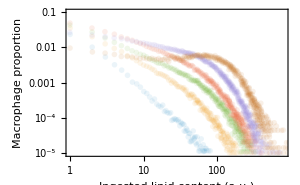

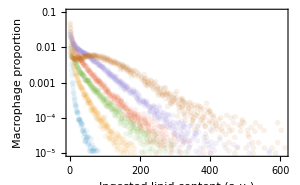

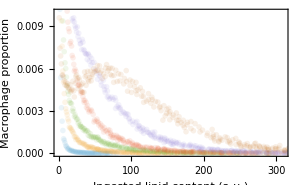

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.1;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,610},{10^(-5),0.3}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,70},{0,0.3(*0.02*)}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
ClearAll[loglikelihood];

loglikelihood[{e_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σL_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodM,loglikelihoodL,outcome,λ,Loutput},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,ee_,idx_?VectorQ,n_?IntegerQ]:=Module[{betaBar,etaBar,alpha,uptake}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta> *)
alpha=Dot[βvec*(ee+idx),v];(* <beta_i (e+i)> *)
uptake=Prepend[Most[v],0]-v;(* m_{i-1} - m_{i} for i>=1*)
alpha *uptake+(betaBar-βvec)*v
];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(β0+β1*idx);
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)


ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(pmf[#,λ]&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,e,idx,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,5}];
loglikelihoodL=Sum[-Log[lipiddata[[i]][[2]]*σL*Sqrt[2 Pi]]-1/(2*σL^2)*(Log[lipiddata[[i]][[2]]]-Log[Loutput[[i]]])^2,{i,2,5}];

If[outcome==0&&Element[loglikelihoodM+loglikelihoodL,Reals],loglikelihoodM+loglikelihoodL,-10^(6)]
]

(* Log-likelihood function *)

plots[{e_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σL_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,Loutput,modeldistributionplotloglinear,modeldistributionplotloglog},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,ηvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ]:=Module[{betaBar,etaBar,alpha,uptake}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta> *)
alpha=Dot[βvec*(ee+idx),v];(* <beta_i (e+i)> *)
uptake=Prepend[Most[v],0]-v;(* m_{i-1} - m_{i} for i>=1*)
alpha *uptake+(betaBar-βvec)*v
];

imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(β0+β1*idx);
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)




ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(pmf[#,λ]&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];

eqs={u'[t]==rhsVecfunction[u[t],βvec,ηvec,fvec,e,fbar,idx,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];


modeldistributionplot=ListPlot[moutput,PlotRange->{{0,300},{0,All}},ImageSize->300,Joined->True];
modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,50},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,50},PlotRange->{{-0.5,50},{-0.05,50}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean ingested lipid (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];


Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot]},{Show[distributionlinearplot48,modeldistributionplot],Show[distributionloglinearplot48,modeldistributionplotloglinear](*,Show[distributionloglogplot48,modeldistributionplotloglog]*)}}]
]
```

```mathematica
(* MLE: βvec = β0 *)
nstep=1;
{eval,β0val,σMval,σmval}={0.4,0.1,1,0.5};
NMaximize[{loglikelihood[{100*e,β0/100,0,1,σM,σL}],0.01<e<1,0.001<β0<1,0.01<σM<3,0.01<σL<1},{e,β0,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,β0val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,β0,σM,σL},loglikelihood[{100*e,β0/100,0,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.532558,0.67753,0.785237,0.470499},-8.0339}

Current x: {{0.524432,0.688797,0.805717,0.474714},-8.03004}

{-8.03004,{e→0.524455,β0→0.688774,σM→0.805685,σL→0.474704}}

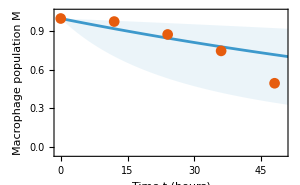
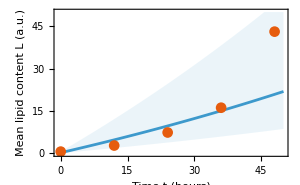
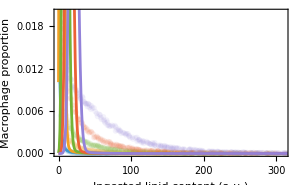
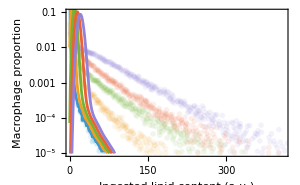
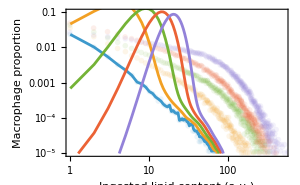
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,β0/100,0,1,σM,σL}/.{e->0.524454586054027,β0->0.6887736938713485,σM->0.8056848649132706,σL->0.4747038600985703}]
```

```mathematica
(* MLE: βvec = β0*Exp[β1*t] *)
nstep=1;
{eval,β0val,β1val,σMval,σmval}={0.5506745397260328,0.2516690091341298,0.053021907234626894,0.3292106669860082,0.05363073479409445};
NMaximize[{loglikelihood[{100*e,β0/100,β1,1,σM,σL}],0.01<e<1,0.001<β0<1,0.001<β1<1,0.01<σM<3,0.01<σL<1},{e,β0,β1,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,β0,β1,σM,σL},loglikelihood[{100*e,β0/100,β1,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.550675,0.251669,0.0530219,0.329211,0.0536307},4.26235}

{4.2624,{e→0.550584,β0→0.251757,β1→0.0530123,σM→0.330339,σL→0.0535789}}

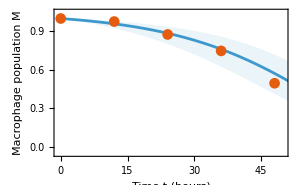
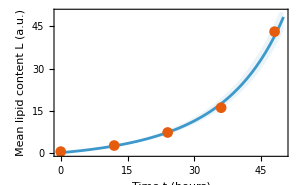
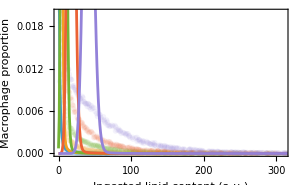
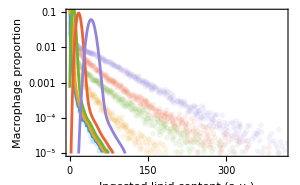
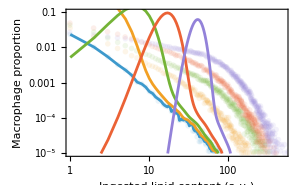
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,β0/100,β1,1,σM,σL}/.{e->0.55058414855106,β0->0.251756634130442,β1->0.053012266168034006,σM->0.33033876336553664,σL->0.05357891155629299}]
```

```mathematica
(* MLE: βvec = β0+β1*idx *)
nstep=1;
{eval,β0val,β1val,σMval,σLval}={0.4959305540582871,0.28390631986869685,0.0883791064027773,0.3651490144041416,0.027906709567477775};
FindMaximum[{loglikelihood[{100*e,β0/100,β1/100,1,σM,σL}],0.01<e<1,0.01<β0<10,0.01<β1<0.2,0.01<σM<3,0.01<σL<1},{{e,eval},{β0,β0val},{β1,β1val},{σM,σMval},{σL,σLval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,β0,β1,1,σM,σL},loglikelihood[{100*e,β0/100,β1/100,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.495931,0.283906,0.0883791,1,0.365149,0.0279067},6.44403}

Current x: {{0.491497,0.286901,0.0888783,1,0.375336,0.0281013},6.44288}

Current x: {{0.491049,0.287236,0.0889333,1,0.37671,0.0280731},6.44269}

Current x: {{0.493187,0.285814,0.0886749,1,0.370843,0.0276628},6.44479}

Current x: {{0.492946,0.285978,0.0887048,1,0.371128,0.0276602},6.44479}

Current x: {{0.492942,0.285981,0.0887053,1,0.371132,0.0276596},6.44479}

Current x: {{0.493,0.285943,0.0886983,1,0.370976,0.0276487},6.44479}

Current x: {{0.492995,0.285946,0.088699,1,0.37098,0.0276485},6.44479}

Current x: {{0.492999,0.285944,0.0886985,1,0.370971,0.0276479},6.44479}

Current x: {{0.492998,0.285944,0.0886986,1,0.370972,0.0276479},6.44479}

{6.44479,{e→0.492998,β0→0.285944,β1→0.0886986,σM→0.370972,σL→0.0276479}}

```mathematica
nstep=1;
{eval,β0val,β1val,σMval,σLval}={0.4959305540582871,0.28390631986869685,0.0883791064027773,0.3651490144041416,0.027906709567477775};
NMaximize[{loglikelihood[{100*e,β0/100,β1/100,1,σM,σL}],0.01<e<1,0.01<β0<1,0.01<β1<1,0.01<σM<1,0.01<σL<1},{e,β0,β1,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,β0,β1,σM,σL},loglikelihood[{100*e,β0/100,β1/100,1,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.481465,0.296297,0.0895008,0.354775,0.0277094},6.37003}

Current x: {{0.495931,0.283906,0.0883791,0.365149,0.0279067},6.44403}

$Aborted

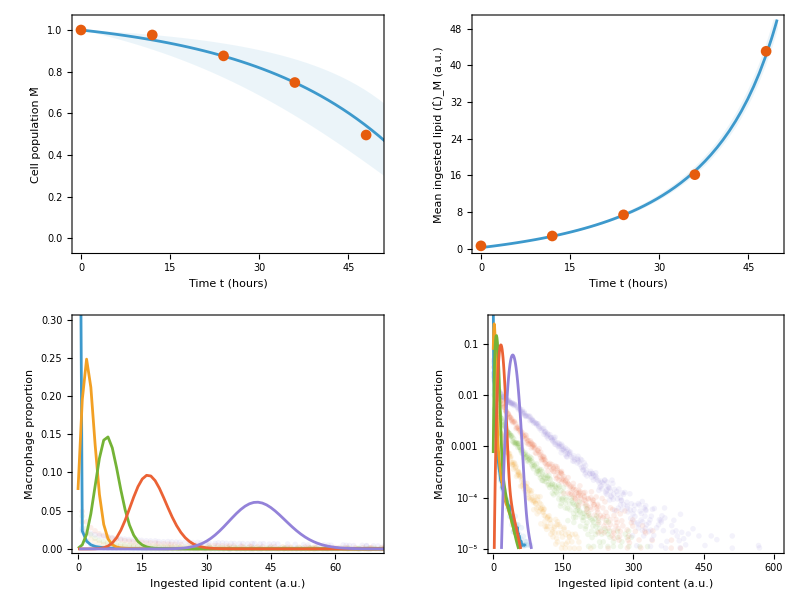

```mathematica
plots[{100*e,β0/100,β1/100,1,σM,σL}/.{e->0.49299820238816017,β0->0.28594410536710463,β1->0.08869858352783742,σM->0.37097154518477393,σL->0.027647902496924552}]
```

```mathematica
(* MLE: βvec = β1/(1+(β1-β0)/β0*Exp[-t/q] - independent of cv! tends to β1->infinity case *)
nstep=1;
{eval,β0val,β1val,qval,σMval,σLval}={0.5524916897698235,0.249752451719019,100.24178638822201,18.64725022610008,0.32900513524462055,0.05525138128518829};
NMaximize[{loglikelihood[{100*e,β0/100,β1/100,q,σM,σL}],0.01<e<1,0.01<β0<1,0.1<β1<1000,0.01<q<100,0.01<σM<3,0.01<σL<1},{e,β0,β1,q,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,β0val,β1val,qval,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,β0,β1,q,σM,σL},loglikelihood[{100*e,β0/100,β1/100,q,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.552492,0.249752,100.242,18.6473,0.329005,0.0536307},4.17838}

Current x: {{0.553627,0.24917,101.198,18.6497,0.332248,0.0546743},4.18101}

$Aborted

```mathematica
{eval,cvval,β0val,β1val,qval,σMval,σLval}={0.74270049747501,0.1,0.09155846845171661,0.9964731101780913,5.334136205905133,0.4778165611630636,0.22784210170928543};
loglikelihood[{100*eval,β0val/100,β1val/100,qval,σMval,σLval}]
```

-3.01191

```mathematica
(* MLE: βvec = β0+(β1-β0)*(1-Exp[-idx/q]. Tends to q->infinity! *)
nstep=1;
{eval,β0val,β1val,qval,σMval,σLval}={0.5427521334057405,0.24118980915658628,9.4829999046745,99.91106305874985,0.33769787819302943,0.04674486752714667};
NMaximize[{loglikelihood[{100*e,β0/100,β1/100,q,σM,σL}],0.01<e<1,0.01<β0<1,0.1<β1<100,0.01<q<1000,0.01<σM<3,0.01<σL<1},{e,β0,β1,q,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,β0val,β1val,qval,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,β0,β1,q,σM,σL},loglikelihood[{100*e,β0/100,β1/100,q,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.542752,0.24119,9.483,99.9111,0.337698,0.0536307},4.73545}

Current x: {{0.541639,0.239676,9.50525,99.5081,0.332752,0.0506104},4.76574}

Current x: {{0.541178,0.240544,9.57311,100.134,0.325668,0.0497076},4.78336}

Current x: {{0.54315,0.249906,12.4568,137.114,0.342525,0.0477347},5.03694}

Current x: {{0.52156,0.268008,21.8953,247.152,0.385873,0.0366012},5.50855}

Current x: {{0.507359,0.27236,23.509,257.483,0.352631,0.0325556},5.7088}

Current x: {{0.48816,0.286044,30.6682,330.757,0.396619,0.0313472},5.84169}

Current x: {{0.459371,0.306788,39.6,413.308,0.412341,0.0288919},5.90949}

Current x: {{0.449417,0.314171,43.1338,443.921,0.423813,0.0280286},5.92176}

Current x: {{0.439302,0.323037,47.2428,480.433,0.439837,0.0272191},5.92624}

$Aborted

```mathematica
loglikelihood[{100*e,β0/100,β1/100,q,σM,σL}/.{e->0.45,β0->0.25,β1->2.5,q->10,σM->0.5,σL->0.5}]
```

-6.11786

```mathematica
{eval,β0val,β1val,qval,σMval,σLval}={0.5524916897698235,0.249752451719019,100.24178638822201,18.64725022610008,0.32900513524462055,0.05525138128518829};
```